## SINGULARITY AT THE DEMISE OF A BLACK HOLE

## SADDLE POINT GEOMETRIES

NOTEBOOK 2 of 2

This notebook is supplementary material for the paper
Singularity at the demise of a black hole
	by Justin C. Feng* and Shinji Mukohyama and Sante Carloni
	["arxiv:2310.17266"](https://arxiv.org/abs/2310.17266) [gr-qc]

This notebook was written in Mathematica 12.2.0.0.

*jcfeng@ntu.edu.tw

## FUNCTIONS

### CONNECTION COEFFICIENTS

This function calculates the connection coefficients:

```mathematica
Gamcalc[g_,X_,n_]:=Module[{Gam,gin},
gin=Inverse[g];
Gam=Table[(1/2)*Sum[gin[[ki,li]]*(D[g[[li,bi]],X[[ai]]]+D[g[[ai,li]],X[[bi]]]-D[g[[ai,bi]],X[[li]]]),{li,1,n}],{ki,1,n},{ai,1,n},{bi,1,n}];
Gam];
```

### COVARIANT DERIVATIVE CALCULATORS

#### RANK ONE DERIVATIVE

##### LOWERED INDEX

This function calculates the covariant derivative of a lowered index vector:

```mathematica
CDVLcalc[V_,g_,X_,n_]:=Module[{Gam},
Gam=Gamcalc[g,X,n];
Table[D[V[[ai]],X[[bi]]]-Sum[Gam[[si,bi,ai]]V[[si]],{si,1,n}],{ai,1,n},{bi,1,n}]];
```

```mathematica
CDVLcalcDIFG[V_,g_,X_,Gam_,n_]:=Module[{},
Table[D[V[[ai]],X[[bi]]]-Sum[Gam[[si,bi,ai]]V[[si]],{si,1,n}],{bi,1,n},{ai,1,n}]];
```

##### RAISED INDEX

This function calculates the covariant derivative of a raised index vector:

```mathematica
CDVRcalc[V_,g_,X_,n_]:=Module[{Gam},
Gam=Gamcalc[g,X,n];
Table[D[V[[ai]],X[[bi]]]+Sum[Gam[[ai,bi,si]]V[[si]],{si,1,n}],{ai,1,n},{bi,1,n}]];
```

#### RANK TWO DERIVATIVE

##### LOWERED INDEX

This function calculates the covariant derivative of a lowered index tensor:

```mathematica
CDT2Lcalc[T_,g_,X_,n_]:=Module[{Gam},
Gam=Gamcalc[g,X,n];
Table[D[T[[ai,bi]],X[[ki]]]-Sum[Gam[[si,ki,ai]]T[[si,bi]]+Gam[[si,ki,bi]]T[[ai,si]],{si,1,n}],{ai,1,n},{bi,1,n},{ki,1,n}]];
```

```mathematica
CDT2LcalcDIF[T_,g_,X_,n_]:=Module[{Gam},
Gam=Gamcalc[g,X,n];
Table[D[T[[ai,bi]],X[[ki]]]-Sum[Gam[[si,ki,ai]]T[[si,bi]]+Gam[[si,ki,bi]]T[[ai,si]],{si,1,n}],{ki,1,n},{ai,1,n},{bi,1,n}]];
```

```mathematica
CDT2LcalcDIFG[T_,g_,X_,Gam_,n_]:=Module[{},
Table[D[T[[ai,bi]],X[[ki]]]-Sum[Gam[[si,ki,ai]]T[[si,bi]]+Gam[[si,ki,bi]]T[[ai,si]],{si,1,n}],{ki,1,n},{ai,1,n},{bi,1,n}]];
```

##### RAISED INDEX

This function calculates the covariant derivative of a raised index tensor:

```mathematica
CDT2Rcalc[T_,g_,X_,n_]:=Module[{Gam},
Gam=Gamcalc[g,X,n];
Table[D[T[[ai,bi]],X[[ki]]]+Sum[Gam[[ai,ki,si]]T[[si,bi]]+Gam[[bi,ki,si]]T[[ai,si]],{si,1,n}],{ai,1,n},{bi,1,n},{ki,1,n}]];
```

#### RANK THREE DERIVATIVE

##### LOWERED INDEX

This function calculates the covariant derivative of a lowered index tensor:

```mathematica
CDT3Lcalc[T_,g_,X_,n_]:=Module[{Gam},
Gam=Gamcalc[g,X,n];
Table[D[T[[ai,bi,ci]],X[[ki]]]-Sum[Gam[[si,ki,ai]]T[[si,bi,ci]]+Gam[[si,ki,bi]]T[[ai,si,ci]]+Gam[[si,ki,ci]]T[[ai,bi,si]],{si,1,n}],{ai,1,n},{bi,1,n},{ci,1,n},{ki,1,n}]];
```

```mathematica
CDT3LcalcDIF[T_,g_,X_,n_]:=Module[{Gam},
Gam=Gamcalc[g,X,n];
Table[D[T[[ai,bi,ci]],X[[ki]]]-Sum[Gam[[si,ki,ai]]T[[si,bi,ci]]+Gam[[si,ki,bi]]T[[ai,si,ci]]+Gam[[si,ki,ci]]T[[ai,bi,si]],{si,1,n}],{ki,1,n},{ai,1,n},{bi,1,n},{ci,1,n}]];
```

```mathematica
CDT3LcalcDIFG[T_,g_,X_,Gam_,n_]:=Module[{},
Table[D[T[[ai,bi,ci]],X[[ki]]]-Sum[Gam[[si,ki,ai]]T[[si,bi,ci]]+Gam[[si,ki,bi]]T[[ai,si,ci]]+Gam[[si,ki,ci]]T[[ai,bi,si]],{si,1,n}],{ki,1,n},{ai,1,n},{bi,1,n},{ci,1,n}]];
```

##### RAISED INDEX

This function calculates the covariant derivative of a raised index tensor:

```mathematica
CDT3Rcalc[T_,g_,X_,n_]:=Module[{Gam},
Gam=Gamcalc[g,X,n];
Table[D[T[[ai,bi,ci]],X[[ki]]]+Sum[Gam[[ai,ki,si]]T[[si,bi,ci]]+Gam[[bi,ki,si]]T[[ai,si,ci]]+Gam[[ci,ki,si]]T[[ai,bi,si]],{si,1,n}],{ai,1,n},{bi,1,n},{ci,1,n},{ki,1,n}]];
```

#### RANK FOUR DERIVATIVE

##### LOWERED INDEX

This function calculates the covariant derivative of a lowered index tensor:

```mathematica
CDT4Lcalc[T_,g_,X_,n_]:=Module[{Gam},
Gam=Gamcalc[g,X,n];
Table[D[T[[ai,bi,ci,di]],X[[ki]]]-Sum[Gam[[si,ki,ai]]T[[si,bi,ci,di]]+Gam[[si,ki,bi]]T[[ai,si,ci,di]]+Gam[[si,ki,ci]]T[[ai,bi,si,di]]+Gam[[si,ki,di]]T[[ai,bi,ci,si]],{si,1,n}],{ai,1,n},{bi,1,n},{ci,1,n},{di,1,n},{ki,1,n}]];
```

##### RAISED INDEX

This function calculates the covariant derivative of a raised index tensor:

```mathematica
CDT4Rcalc[T_,g_,X_,n_]:=Module[{Gam},
Gam=Gamcalc[g,X,n];
Table[D[T[[ai,bi,ci,di]],X[[ki]]]+Sum[Gam[[ai,ki,si]]T[[si,bi,ci,di]]+Gam[[bi,ki,si]]T[[ai,si,ci,di]]+Gam[[ci,ki,si]]T[[ai,bi,si,di]]+Gam[[di,ki,si]]T[[ai,bi,ci,si]],{si,1,n}],{ai,1,n},{bi,1,n},{ci,1,n},{di,1,n},{ki,1,n}]];
```

### RIEMANN CALCULATOR

#### RIEMANN TENSOR

```mathematica
Riemanncalc[g_,X_,n_]:=Module[{Gam},
Gam=Gamcalc[g,X,n];
Table[D[Gam[[ii,bi,ji]],X[[ai]]]-D[Gam[[ii,ai,ji]],X[[bi]]]+Sum[Gam[[ii,ai,si]]*Gam[[si,bi,ji]]-Gam[[ii,bi,si]]*Gam[[si,ai,ji]],{si,1,n}],{ii,1,n},{ji,1,n},{ai,1,n},{bi,1,n}]];
```

```mathematica
(*  *)
RiemanncalcS[g_,Gam_,X_,n_]:=Module[{},
Table[D[Gam[[ii,bi,ji]],X[[ai]]]-D[Gam[[ii,ai,ji]],X[[bi]]]+Sum[Gam[[ii,ai,si]]*Gam[[si,bi,ji]]-Gam[[ii,bi,si]]*Gam[[si,ai,ji]],{si,1,n}],{ii,1,n},{ji,1,n},{ai,1,n},{bi,1,n}]];
```

#### RIEMANN TENSOR IN ALL LOWERED INDICES

```mathematica
RiemannLcalc[g_,X_,n_]:=Module[{Riemann},
Riemann=Riemanncalc[g,X,n];
Table[Sum[g[[ii,si]]*Riemann[[si,ji,ai,bi]],{si,1,n}],{ii,1,n},{ji,1,n},{ai,1,n},{bi,1,n}]];
```

```mathematica
(*  *)
RiemannLcalcS[g_,Riemann_,X_,n_]:=Module[{},
Table[Sum[g[[ii,si]]*Riemann[[si,ji,ai,bi]],{si,1,n}],{ii,1,n},{ji,1,n},{ai,1,n},{bi,1,n}]];
```

#### RIEMANN TENSOR IN ALL RAISED INDICES

```mathematica
RiemannUcalc[g_,X_,n_]:=Module[{Riemann,gin},
Riemann=Riemanncalc[g,X,n];
gin=Inverse[g];
Table[Sum[gin[[ji,si]]*gin[[ai,mi]]*gin[[bi,ni]]*Riemann[[ii,si,mi,ni]],{si,1,n},{mi,1,n},{ni,1,n}],{ii,1,n},{ji,1,n},{ai,1,n},{bi,1,n}]];
```

```mathematica
(*  *)
RiemannUcalcS[g_,gin_,Riemann_,X_,n_]:=Module[{},
Table[Sum[gin[[ji,si]]*gin[[ai,mi]]*gin[[bi,ni]]*Riemann[[ii,si,mi,ni]],{si,1,n},{mi,1,n},{ni,1,n}],{ii,1,n},{ji,1,n},{ai,1,n},{bi,1,n}]];
```

#### RIEMANN TENSOR (FIRST TWO RAISED)

```mathematica
RiemannU1calc[g_,X_,n_]:=Module[{Riemann,gin},
Riemann=Riemanncalc[g,X,n];
gin=Inverse[g];
Table[Sum[gin[[ji,si]]*Riemann[[ii,si,ai,bi]],{si,1,n}],{ii,1,n},{ji,1,n},{ai,1,n},{bi,1,n}]];
```

```mathematica
(*  *)
RiemannU1calcS[g_,gin_,Riemann_,X_,n_]:=Module[{},
Table[Sum[gin[[ji,si]]*Riemann[[ii,si,ai,bi]],{si,1,n}],{ii,1,n},{ji,1,n},{ai,1,n},{bi,1,n}]];
```

#### RIEMANN TENSOR (SECOND TWO RAISED)

```mathematica
RiemannU2calc[g_,X_,n_]:=Module[{RiemannL,gin},
RiemannL=RiemannLcalc[g,X,n];
gin=Inverse[g];
Table[Sum[gin[[ai,mi]]*gin[[bi,ni]]*RiemannL[[ii,ji,mi,ni]],{mi,1,n},{ni,1,n}],{ii,1,n},{ji,1,n},{ai,1,n},{bi,1,n}]];
```

```mathematica
(*  *)
RiemannU2calcS[g_,gin_,RiemannL_,X_,n_]:=Module[{},
Table[Sum[gin[[ai,mi]]*gin[[bi,ni]]*RiemannL[[ii,ji,mi,ni]],{mi,1,n},{ni,1,n}],{ii,1,n},{ji,1,n},{ai,1,n},{bi,1,n}]];
```

### RICCI CALCULATOR

#### RICCI TENSOR

This function calculates the Ricci curvature in lowered indices:

```mathematica
RicciLcalc[g_,X_,n_]:=Module[{Gam},
Gam=Gamcalc[g,X,n];
Table[Sum[D[Gam[[ai,ii,ji]],X[[ai]]]-D[Gam[[ai,ai,ji]],X[[ii]]]+Sum[Gam[[ai,ai,si]]*Gam[[si,ii,ji]]-Gam[[ai,ii,si]]*Gam[[si,ai,ji]],{si,1,n}],{ai,1,n}],{ii,1,n},{ji,1,n}]];
```

```mathematica
RicciLcalcG[g_,X_,Gam_,n_]:=Module[{},
Table[Sum[D[Gam[[ai,ii,ji]],X[[ai]]]-D[Gam[[ai,ai,ji]],X[[ii]]]+Sum[Gam[[ai,ai,si]]*Gam[[si,ii,ji]]-Gam[[ai,ii,si]]*Gam[[si,ai,ji]],{si,1,n}],{ai,1,n}],{ii,1,n},{ji,1,n}]];
```

#### RICCI SCALAR

This function calculates the Ricci scalar:

```mathematica
RicciScalc[g_,X_,n_]:=Module[{gin,Ricci},
gin=Inverse[g];
Ricci=RicciLcalc[g,X,n];
Sum[gin[[ii,ji]]Ricci[[ii,ji]],{ii,1,n},{ji,1,n}]];
```

#### EINSTEIN TENSOR

```mathematica
(* EINSTEIN TENSOR *)
EinsteinLcalc[g_,X_,n_]:=Module[{Ricci,R},
Ricci=RicciLcalc[g,X,n];
R=RicciScalc[g,X,n];
Table[(Ricci[[ai,bi]]-R/2 g[[ai,bi]]),{ai,1,n},{bi,1,n}]];
```

## GEOMETRY

### INITIALIZATION

Clearing variables and setting dimension

```mathematica
(* CLEAR VARIABLES *)
Clear[d,X,g,gin,Gam,RiemL,RicL,Rs,φ,dφ,ddφ,geff,gineff,Detgeff]
Clear[X4,geff4,gineff4,Xs,e,NT];
Clear[ai,bi,ci,di,ii,ji,ki,li,si];

(* DIMENSIONS *)
d=2;
```

### METRIC CONSTRUCTION & ASSUMPTIONS

#### CONSTRUCTION

Specifying coordinates, metric and assumptions. Schwarzschild metric given as an example.

```mathematica
(* COORDINATES *)
X={u,v};
dX={du,dv};

(* METRIC *)
g=({{1, 0}, {0, 1}});
gin=Inverse[g];

(* ASSUMPTIONS *)
assum={X∈Reals,r>0,0<θ<π,0<ψ<π,F[a]∈Reals,S[a]>0};
```

```mathematica
dX.(g.dX)//Simplify
```

du^2+dv^2

### INVERSE & CONNECTION

Inverse metric and connection are computed here.

```mathematica
(* INVERSE METRIC *)
gin=Simplify[Inverse[g],Assumptions->assum];

(* CONNECTION COEFFICIENTS *)
Gam=Simplify[Gamcalc[g,X,d],Assumptions->assum];
```

### CURVATURE

#### LOWERED INDEX EXPRESSIONS

##### EVALUATION

```mathematica
Rs=RicciScalc[g,X,d]//FullSimplify;
RicL=RicciLcalc[g,X,d]//FullSimplify;
RiemL=RiemannLcalc[g,X,d]//FullSimplify;
```

##### DISPLAY

```mathematica
Rs
```

0

```mathematica
RicL//MatrixForm
```

(0 | 0
0 | 0)

```mathematica
RiemL
```

{{{{0,0},{0,0}},{{0,0},{0,0}}},{{{0,0},{0,0}},{{0,0},{0,0}}}}

### EFFECTIVE METRIC

#### SCALAR FIELD PROFILE

##### SCALAR FIELD

CONSTRUCTION

```mathematica
φ=(u^2-v^2)/(2l0);
```

GRADIENT

```mathematica
dφ=Table[D[φ,X[[ii]]],{ii,1,d}];
```

SECOND DERIVATIVE

```mathematica
ddφ=CDVLcalc[dφ,g,X,d];
```

```mathematica
ddφ//MatrixForm
```

(1/l0 | 0
0 | -1/l0)

TRACE OF SECOND DERIVATIVE

```mathematica
ddφmx=gin.ddφ;
```

```mathematica
Tr[ddφmx.ddφmx]
```

2/l0^2

BACKGROUND GRADIENT NORM

```mathematica
χ=dφ.(gin.dφ)//FullSimplify;
```

##### CONTOUR PLOTS

PLOT VARIABLES

```mathematica
plotdomain=0.01;
```

SCALAR FIELD PLOT

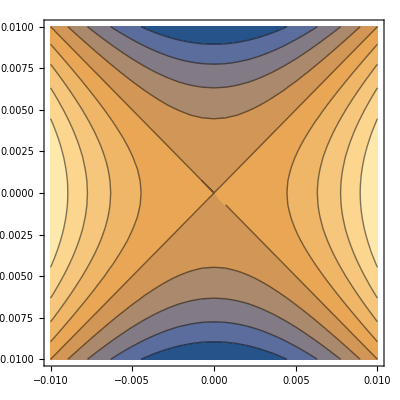

```mathematica
ContourPlot[φ/.{l0->1},{u,-plotdomain,plotdomain},{v,-plotdomain,plotdomain}]
```

BACKGROUND NORM PLOT

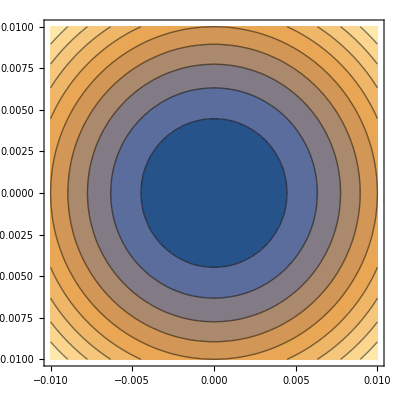

```mathematica
ContourPlot[χ/.{l0->1},{u,-plotdomain,plotdomain},{v,-plotdomain,plotdomain}]
```

#### EFFECTIVE METRIC

##### RULES

```mathematica
repscoupling={XC->(ρ0/l0)^2};
```

##### CONSTRUCTION

MAIN

```mathematica
geff=g-1/(XC)Table[dφ[[ii]]dφ[[ji]],{ii,1,d},{ji,1,d}]//FullSimplify;
geff//MatrixForm
```

(1-u^2/(l0^2 XC) | (u v)/(l0^2 XC)
(u v)/(l0^2 XC) | 1-v^2/(l0^2 XC))

```mathematica
gineff=Inverse[geff]//FullSimplify;
```

COUPLING REPLACEMENTS

```mathematica
geff/.repscoupling//FullSimplify//MatrixForm
```

(1-u^2/ρ0^2 | (u v)/ρ0^2
(u v)/ρ0^2 | 1-v^2/ρ0^2)

##### RICCI CURVATURE

2D CASE

```mathematica
RicLeff=RicciLcalc[geff,X,d]//FullSimplify;
```

```mathematica
gineff.RicLeff/.repscoupling/.{u^2->ρ^2-v^2}//FullSimplify//MatrixForm
Limit[%,ρ->∞]//MatrixForm
```

(ρ0^2/((ρ^2-ρ0^2)^2) | 0
0 | ρ0^2/((ρ^2-ρ0^2)^2))

(0 | 0
0 | 0)

4D CASE

```mathematica
X4={u,v,y,z};
geff4=({{1-u^2/ρ0^2, (u v)/ρ0^2, 0, 0}, {(u v)/ρ0^2, 1-v^2/ρ0^2, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}});
gineff4=Inverse[geff4]//FullSimplify;
RicLeff4=RicciLcalc[geff4,X4,4]//FullSimplify;
```

```mathematica
gineff4.RicLeff4/.repscoupling/.{u^2->ρ^2-v^2}//FullSimplify//MatrixForm
Limit[%,ρ->∞]//MatrixForm
```

(ρ0^2/((ρ^2-ρ0^2)^2) | 0 | 0 | 0
0 | ρ0^2/((ρ^2-ρ0^2)^2) | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

##### DETERMINANT AND DEGENERATE SURFACE

CONSTRUCTION

```mathematica
Detgeff=Det[geff]
```

1-u^2/(l0^2 XC)-v^2/(l0^2 XC)

DEGENERATE SURFACE CONDITION

```mathematica
Detgeff/.repscoupling
%==0;
Solve[%,ρ0][[2]];
ρ0^2==(ρ0^2/.%)
```

1-u^2/ρ0^2-v^2/ρ0^2

ρ0^2==u^2+v^2

##### TANGENT VECTOR

PARAMETERIZED SURFACE

```mathematica
Xs=ρ0{Sin[ϑ],Cos[ϑ]};
```

PROJECTION OPERATOR

```mathematica
e=D[Xs,ϑ]
```

{ρ0 Cos[ϑ],-ρ0 Sin[ϑ]}

NORM TANGENT

```mathematica
NT=e.(geff.e)/.{u->Xs[[1]],v->Xs[[2]]}/.repscoupling//FullSimplify
```

ρ0^2 Cos[2 ϑ]^2

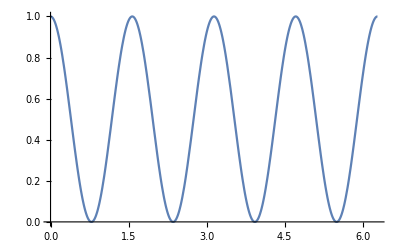

```mathematica
Plot[NT/.{ρ0->1},{ϑ,0,2π}]
```